Initial Truss Diagram:

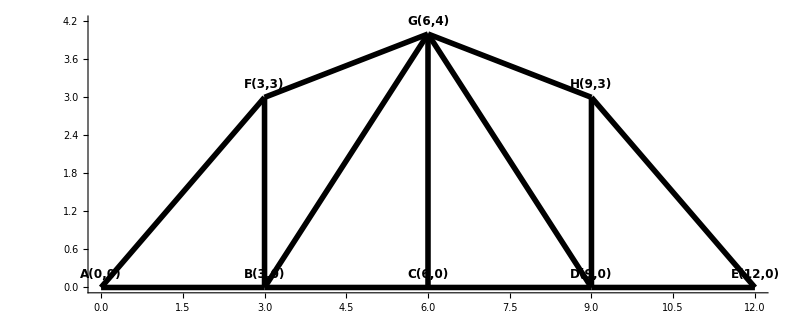

Applied External Forces (N):

A: {10,5}

B: {0,0}

C: {5,15}

D: {0,0}

E: {0,0}

F: {0,0}

G: {0,0}

H: {0,0}

Global Reaction Forces:

At A (roller):  (Ax=0, Ay) = {0, -12.500}  N

At E (fixed):   (Ex, Ey) = {-15.000, -7.500}  N

Internal Member Forces (N):

FAB: -17.500

FBC: -21.250

FCD: -26.250

FDE: -22.500

FAF: 10.607

FBF: -5.000

FFG: 7.906

FCG: -15.000

FGH: 7.906

FDH: -5.000

FHE: 10.607

FBG: 6.250

FDG: 6.250

Truss Force Diagram:

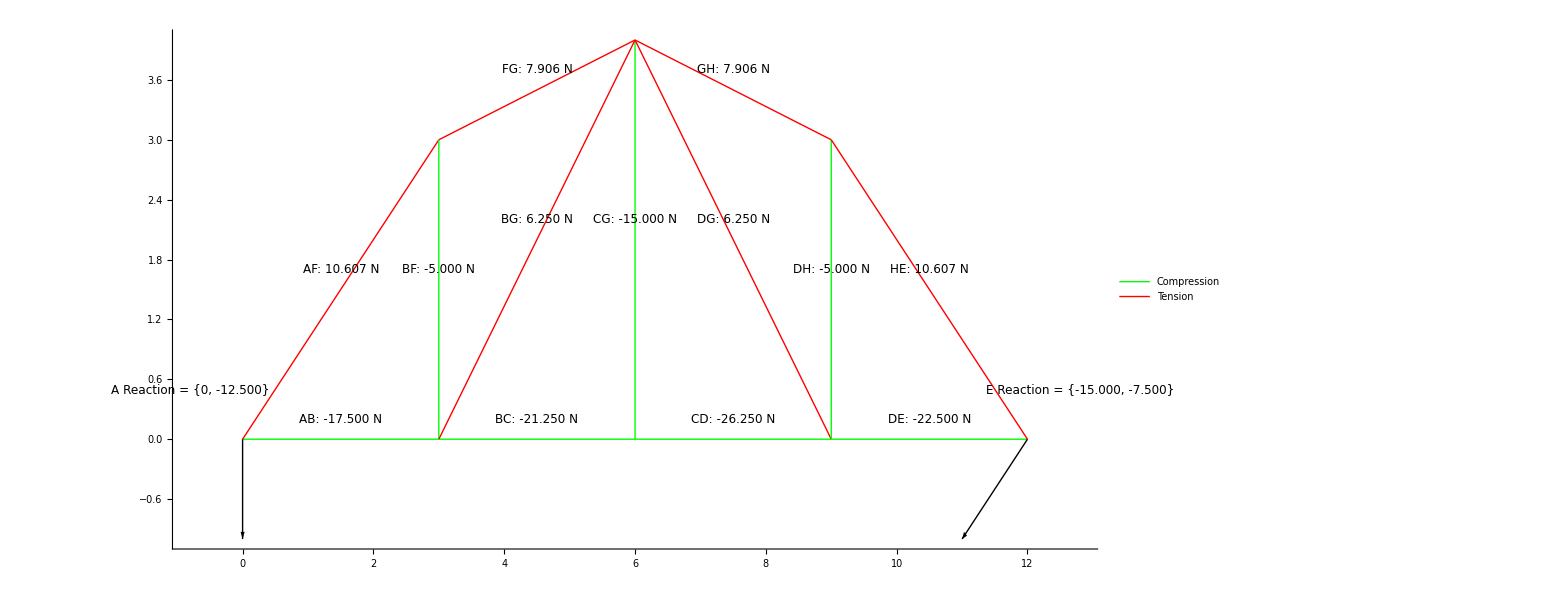

```mathematica
(*1) Clear all and define the unknown \
force symbols for the 13 members*)(*plus reaction forces at A (Ay) \
and E (Ex,
  Ey).*)(* \
=====================================================================\
[Equal]*)ClearAll["Global`*"];

Clear[FAB, FBC, FCD, FDE, FAF, FBF, FFG, FCG, FGH, FDH, FHE, FBG, 
  FDG,(*New members:B->G and D->G*)Ay, Ex, Ey];

(* \
=====================================================================\
[Equal]*)
(*2) Define node positions and the connectivity for your 8-node \
truss.*)
(*We add two new connections:B->G and D->G.*)
(* \
=====================================================================\
[Equal]*)
positions = <|"A" -> {0, 0}, "B" -> {3, 0}, "C" -> {6, 0}, 
   "D" -> {9, 0}, "E" -> {12, 0}, "F" -> {3, 3}, "G" -> {6, 4}, 
   "H" -> {9, 3}|>;

connections = {{"A", "B"}, {"B", "C"}, {"C", "D"}, {"D", 
    "E"},(*bottom chord*){"A", "F"}, {"B", "F"}, {"F", "G"}, {"C", 
    "G"}, {"G", "H"}, {"D", "H"}, {"H", "E"},(*top+
   webs*){"B", "G"}, {"D", "G"}  (*newly added connections*)};

(* \
=====================================================================\
[Equal]*)
(*3) Draw the initial truss diagram with labeled nodes*)
(* \
=====================================================================\
[Equal]*)
drawTruss[labelNodes_: True] := 
  Module[{lines, nodeLabels}, 
   lines = {Line[{positions[#1], positions[#2]}] & @@@ connections};
   nodeLabels = 
    If[labelNodes, 
     Table[Text[
       Style[pt <> "(" <> ToString[positions[pt][[1]]] <> "," <> 
         ToString[positions[pt][[2]]] <> ")", 12, Bold], 
       positions[pt] + {0, 0.2}], {pt, Keys[positions]}], {}];
   Graphics[{Thickness[0.005], lines, nodeLabels}, Axes -> True, 
    PlotRange -> All, AspectRatio -> Automatic, 
    ImageSize -> 
     800  (*Increase image size for a bigger truss diagram*)]];

Print["Initial Truss Diagram:"];
Print[drawTruss[]];

(* \
=====================================================================\
[Equal]*)
(*4) Ask user for external forces in the format:node Fx Fy node Fx Fy...*)
\

(* \
=====================================================================\
[Equal]*)
externalForces = 
  AssociationThread[
   Keys[positions] -> Table[{0, 0}, {Length[positions]}]];

forceInput = 
  InputString[
   "Enter forces in 'Node Fx Fy Node Fx Fy' format (e.g. 'A 10 5 C -5 15'): "];
words = StringSplit[forceInput];
nTriples = Floor[Length[words]/3];

Do[Module[{node, fx, fy}, node = ToUpperCase[words[[3*i - 2]]];
   fx = ToExpression[words[[3*i - 1]]];
   fy = ToExpression[words[[3*i]]];
   If[KeyExistsQ[externalForces, node], 
    externalForces[node] += {fx, fy}, 
    Print["Warning: Node ", node, " is invalid. Skipping..."]]], {i, 
   1, nTriples}];

Print["\nApplied External Forces (N):"];
Do[Print[pt, ": ", externalForces[pt]], {pt, Keys[positions]}];

(* \
=====================================================================\
[Equal]*)
(*5) Compute support reactions at A (roller=>only Ay) and E (Ex,Ey)*)
\

(*using overall equilibrium:sum(Fx)=0,sum(Fy)=0,sum(Moments=0).*)
(* \
=====================================================================\
[Equal]*)
totalExt = Total[Values[externalForces]];
extFx = totalExt[[1]];
extFy = totalExt[[2]];

(*Sum of moments of external forces about A:M=x*Fy-y*Fx.*)
momentExt = 0;
Do[With[{pos = positions[pt], F = externalForces[pt]}, 
   momentExt += (pos[[1]]*F[[2]] - pos[[2]]*F[[1]]);], {pt, 
   Keys[positions]}];

(*Roller at A=>Ax=0=>Ex=-extFx.*)
Ex = -extFx;
posE = positions["E"];
Ey = (-momentExt + posE[[2]]*Ex)/posE[[1]];
Ay = -extFy - Ey;

(*Force them to decimal.*)
Ex = N[Ex, 6];
Ey = N[Ey, 6];
Ay = N[Ay, 6];

Print["\nGlobal Reaction Forces:"];
Print["At A (roller):  (Ax=0, Ay) = {0, ", NumberForm[Ay, {6, 3}], 
  "}  N"];
Print["At E (fixed):   (Ex, Ey) = {", NumberForm[Ex, {6, 3}], ", ", 
  NumberForm[Ey, {6, 3}], "}  N"];

(* \
=====================================================================\
[Equal]*)
(*6) Method of Joints:define unit vectors and set up equilibrium.*)
(* \
=====================================================================\
[Equal]*)
uAB = Normalize[positions["B"] - positions["A"]];
uBC = Normalize[positions["C"] - positions["B"]];
uCD = Normalize[positions["D"] - positions["C"]];
uDE = Normalize[positions["E"] - positions["D"]];
uAF = Normalize[positions["F"] - positions["A"]];
uBF = Normalize[positions["F"] - positions["B"]];
uFG = Normalize[positions["G"] - positions["F"]];
uCG = Normalize[positions["G"] - positions["C"]];
uGH = Normalize[positions["H"] - positions["G"]];
uDH = Normalize[positions["H"] - positions["D"]];
uHE = Normalize[positions["E"] - positions["H"]];
uBG = Normalize[positions["G"] - positions["B"]];
uDG = Normalize[positions["G"] - positions["D"]];

eqA = {FAB*uAB[[1]] + FAF*uAF[[1]] == -externalForces["A"][[1]], 
   FAB*uAB[[2]] + FAF*uAF[[2]] + Ay == -externalForces["A"][[2]]};

eqB = {-FAB*uAB[[1]] + FBC*uBC[[1]] + FBF*uBF[[1]] + 
     FBG*uBG[[1]] == -externalForces["B"][[1]], -FAB*uAB[[2]] + 
     FBC*uBC[[2]] + FBF*uBF[[2]] + 
     FBG*uBG[[2]] == -externalForces["B"][[2]]};

eqC = {-FBC*uBC[[1]] + FCD*uCD[[1]] + 
     FCG*uCG[[1]] == -externalForces["C"][[1]], -FBC*uBC[[2]] + 
     FCD*uCD[[2]] + FCG*uCG[[2]] == -externalForces["C"][[2]]};

eqD = {-FCD*uCD[[1]] + FDE*uDE[[1]] + FDH*uDH[[1]] + 
     FDG*uDG[[1]] == -externalForces["D"][[1]], -FCD*uCD[[2]] + 
     FDE*uDE[[2]] + FDH*uDH[[2]] + 
     FDG*uDG[[2]] == -externalForces["D"][[2]]};

eqE = {-FDE*uDE[[1]] - FHE*uHE[[1]] + 
     Ex == -externalForces["E"][[1]], -FDE*uDE[[2]] - FHE*uHE[[2]] + 
     Ey == -externalForces["E"][[2]]};

eqF = {-FAF*uAF[[1]] - FBF*uBF[[1]] + 
     FFG*uFG[[1]] == -externalForces["F"][[1]], -FAF*uAF[[2]] - 
     FBF*uBF[[2]] + FFG*uFG[[2]] == -externalForces["F"][[2]]};

eqG = {-FFG*uFG[[1]] - FCG*uCG[[1]] - FBG*uBG[[1]] - FDG*uDG[[1]] + 
     FGH*uGH[[1]] == -externalForces["G"][[1]], -FFG*uFG[[2]] - 
     FCG*uCG[[2]] - FBG*uBG[[2]] - FDG*uDG[[2]] + 
     FGH*uGH[[2]] == -externalForces["G"][[2]]};

eqH = {-FGH*uGH[[1]] - FDH*uDH[[1]] + 
     FHE*uHE[[1]] == -externalForces["H"][[1]], -FGH*uGH[[2]] - 
     FDH*uDH[[2]] + FHE*uHE[[2]] == -externalForces["H"][[2]]};

allEqns = Flatten[{eqA, eqB, eqC, eqD, eqE, eqF, eqG, eqH}];

sol = Solve[
   allEqns, {FAB, FBC, FCD, FDE, FAF, FBF, FFG, FCG, FGH, FDH, FHE, 
    FBG, FDG}];

If[sol === {} || Length[sol] > 1, 
  Print["No unique solution or system is over-/under-constrained."], 
  Print["\nInternal Member Forces (N):\n"];
  solVals = Association[sol[[1]]];
  (*Convert each symbolic force to decimal before printing*)
  Do[Print[m, ": ", 
    NumberForm[N[solVals[m], 6], {6, 3}]], {m, {FAB, FBC, FCD, FDE, 
     FAF, FBF, FFG, FCG, FGH, FDH, FHE, FBG, FDG}}];];

(* \
=====================================================================\
[Equal]*)
(*7) Final Graphics:color-coded members in red/green/black,with \
numeric*)
(*(decimal) labels for each force in black,plus a legend.*)
(* \
=====================================================================\
[Equal]*)
colorFor[force_, tol_: 1.*^-4] := 
  Which[force > tol, Red,(*tension*)force < -tol, Green,(*compression*)
   True, Black           (*near zero*)];

(*We define a member list that includes the new members B->G and \
D->G.*)
memberList = {{"AB", FAB, "A", "B"}, {"BC", FBC, "B", "C"}, {"CD", 
    FCD, "C", "D"}, {"DE", FDE, "D", "E"}, {"AF", FAF, "A", 
    "F"}, {"BF", FBF, "B", "F"}, {"FG", FFG, "F", "G"}, {"CG", FCG, 
    "C", "G"}, {"BG", FBG, "B", "G"}, {"DG", FDG, "D", "G"}, {"GH", 
    FGH, "G", "H"}, {"DH", FDH, "D", "H"}, {"HE", FHE, "H", "E"}};

drawTrussSolution[] := 
  Module[{graphicsItems = {}, arrowItems, legendItems}, 
   Do[With[{name = md[[1]], sym = md[[2]], n1 = md[[3]], 
      n2 = md[[4]]}, 
     Module[{fval, col, mid, labelTxt}, 
      fval = N[solVals[sym], 6];(*Force in decimal form*)
      col = colorFor[fval];
      mid = (positions[n1] + positions[n2])/2;
      labelTxt = 
       Text[Style[
         name <> ": " <> ToString[NumberForm[fval, {6, 3}]] <> " N", 
         Black, 12  (*text always black,font size 12*)], 
        mid + {0, 0.2}];
      AppendTo[
       graphicsItems, {col, Thick, 
        Line[{positions[n1], positions[n2]}], labelTxt}];]], {md, 
     memberList}];
   (*Reaction arrows in decimal form as well.*)
   Module[{ayDec, exDec, eyDec}, ayDec = N[Ay, 6];
    exDec = N[Ex, 6];
    eyDec = N[Ey, 6];
    arrowItems = {Arrow[{positions["A"], 
        positions["A"] + {0, ayDec/Max[1, Abs[ayDec]]}}], 
      Text[Style[
        "A Reaction = {0, " <> ToString[NumberForm[ayDec, {6, 3}]] <> 
         "}", 12, Black], positions["A"] + {-0.8, 0.5}], 
      Arrow[{positions["E"], 
        positions["E"] + {exDec/Max[1, Abs[exDec]], 
          eyDec/Max[1, Abs[eyDec]]}}], 
      Text[Style[
        "E Reaction = {" <> ToString[NumberForm[exDec, {6, 3}]] <> 
         ", " <> ToString[NumberForm[eyDec, {6, 3}]] <> "}", 12, 
        Black], positions["E"] + {0.8, 0.5}]};];
   (*Create a simple legend for "Compression" (green) and "Tension" \
(red).*)legendItems = {Inset[
      Grid[{{Graphics[{Green, Thick, Line[{{0, 0}, {1, 0}}]}, 
          ImageSize -> 30], 
         Style["Compression", 
          12]}, {Graphics[{Red, Thick, Line[{{0, 0}, {1, 0}}]}, 
          ImageSize -> 30], Style["Tension", 12]}}, Alignment -> Left,
        Spacings -> {2, 0.8}], Scaled[{0.85, 0.85}],(*place near top-
      right corner*){Right, Top}]};
   Graphics[{graphicsItems, arrowItems, legendItems}, Axes -> True, 
    PlotRange -> All, AspectRatio -> Automatic, ImageSize -> 1500]];

If[sol === {} || Length[sol] > 1, 
  Print["\nNo valid solution to display."], 
  Print["\nTruss Force Diagram:"];
  Print[drawTrussSolution[]];];
```